## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
ClearAll["InversePNUtils`*"]
```

## 设置non-GR参数字符flag

```mathematica
eventFlag="GW150914";
psiFlag="psi";
alphaFlag="alpha";

deviationFlag="cpsi";
deviationOrder="6l";
deviationType="constant";

fileSuffix="";

alphaName=alphaFlag<>ToString[deviationOrder]
psiName=psiFlag<>ToString[deviationOrder]
deviationName=deviationFlag<>ToString[deviationOrder]
modifiedAlphaName=alphaFlag<>ToString[deviationOrder]<>deviationFlag
modifiedPsiName=psiFlag<>ToString[deviationOrder]<>deviationFlag
```

alpha6l

psi6l

cpsi6l

alpha6lcpsi

psi6lcpsi

```mathematica
"alpha3"
```

alpha3

## Prepare Data from CSV or HDF

```mathematica
csvFolder="D:\\Documents\\workspace\\课题\\workspace\\Parameterized_PN_Tests\\csv"<>"\\"<>eventFlag
csvName="OGC4-GW150914_"<>deviationName<>fileSuffix<>".csv"
csvPath=csvFolder<>"\\"<>csvName
```

D:\Documents\workspace\课题\workspace\Parameterized_PN_Tests\csv\GW150914

OGC4-GW150914_cpsi6l.csv

D:\Documents\workspace\课题\workspace\Parameterized_PN_Tests\csv\GW150914\OGC4-GW150914_cpsi6l.csv

### from CSV

```mathematica
CSVSamples=Import[csvPath];

samples=<||>;
samples["mass1"]=CSVSamples[[All,1]][[2;;]];
samples["mass2"]=CSVSamples[[All,2]][[2;;]];
samples["spin1_z"]=CSVSamples[[All,3]][[2;;]];
samples["spin2_z"]=CSVSamples[[All,4]][[2;;]];
samples["eta"]=CSVSamples[[All,5]][[2;;]];
samples["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[deviationName]=CSVSamples[[All,7]][[2;;]];
```

```mathematica
samples["chis"]=χs[samples["spin1_z"],samples["spin2_z"]];
samples["chia"]=χa[samples["spin1_z"],samples["spin2_z"]];
```

### Calculate Coefficients

#### N-Order Coefficients, ψ

```mathematica
samples["psi0"]=MapThread[
Psi[0,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi2"]=MapThread[
Psi[2,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi3"]=MapThread[
Psi[3,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi4"]=MapThread[
Psi[4,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi5"]=MapThread[
Psi[5,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi5l"]=MapThread[
Psi["5l",η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6"]=MapThread[
Psi[6,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6l"]=MapThread[
Psi["6l",η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

```mathematica
Keys[samples]
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,cpsi6l,chis,chia,psi0,psi2,psi3,psi4,psi5,psi5l,psi6,psi6l}

```mathematica
{"mass1","mass2","spin1_z","spin2_z","eta","Mchirp","cpsi4","chis","chia","psi0","psi2","psi3","psi4","psi5","psi5l","psi6","psi6l"}
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,cpsi4,chis,chia,psi0,psi2,psi3,psi4,psi5,psi5l,psi6,psi6l}

## Plot PN Coefficients and Related Parameters

```mathematica
BCI=<||>;
```

### Plots Masses

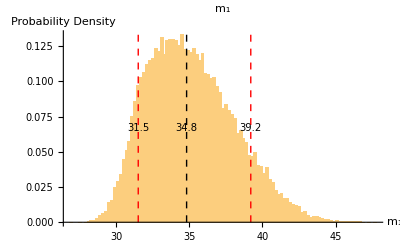

```mathematica
BCI["mass1"]=PlotParameterWithBCI[samples["mass1"],Subscript["m","1"]][[1]];
```

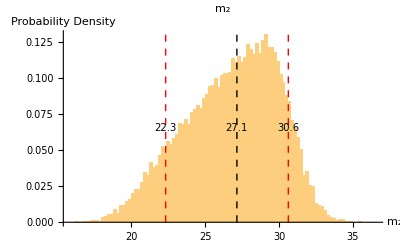

```mathematica
BCI["mass2"]=PlotParameterWithBCI[samples["mass2"],Subscript["m","2"]][[1]];
```

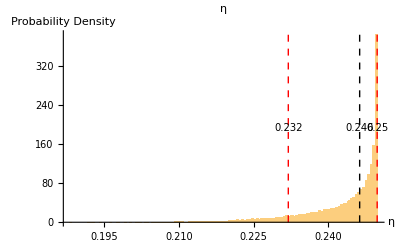

```mathematica
BCI["eta"]=PlotParameterWithBCI[samples["eta"],"η"][[1]];
```

### Plots Spin Components Aligning Orbital Angular Momentum (Then be it spin_z)

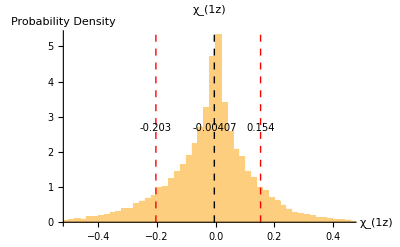

```mathematica
BCI["spin1_z"]=PlotParameterWithBCI[samples["spin1_z"],Subscript["χ","1z"]][[1]];
```

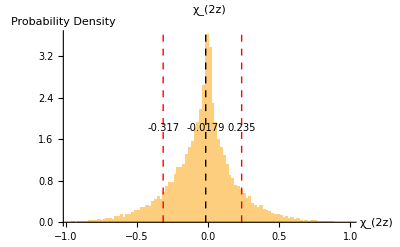

```mathematica
BCI["spin2_z"]=PlotParameterWithBCI[samples["spin2_z"],Subscript["χ","2z"]][[1]];
```

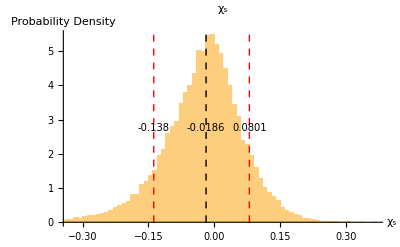

```mathematica
BCI["chis"]=PlotParameterWithBCI[samples["chis"],Subscript["χ","s"]][[1]];
```

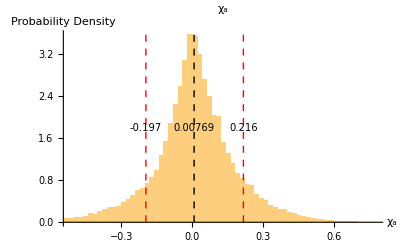

```mathematica
BCI["chia"]=PlotParameterWithBCI[samples["chia"],Subscript["χ","a"]][[1]];
```

### Plot psi

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

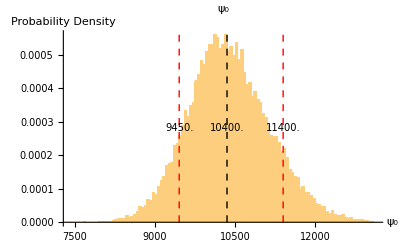

```mathematica
BCI["psi0"]=PlotParameterWithBCI[samples["psi0"],Subscript["ψ","0"]][[1]];
```

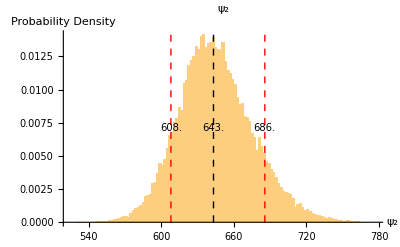

```mathematica
BCI["psi2"]=PlotParameterWithBCI[samples["psi2"],Subscript["ψ","2"]][[1]];
```

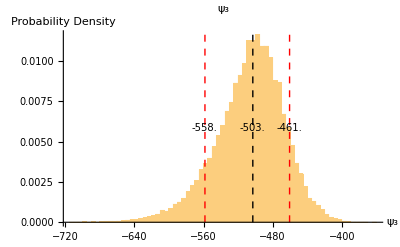

```mathematica
BCI["psi3"]=PlotParameterWithBCI[samples["psi3"],Subscript["ψ","3"]][[1]];
```

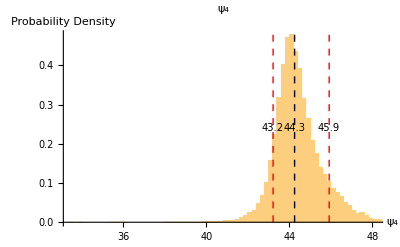

```mathematica
BCI["psi4"]=PlotParameterWithBCI[samples["psi4"],Subscript["ψ","4"]][[1]];
```

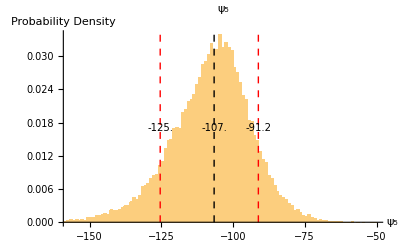

```mathematica
BCI["psi5"]=PlotParameterWithBCI[samples["psi5"],Subscript["ψ","5"]][[1]];
```

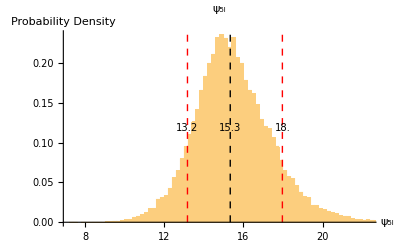

```mathematica
BCI["psi5l"]=PlotParameterWithBCI[samples["psi5l"],Subscript["ψ","5l"]][[1]];
```

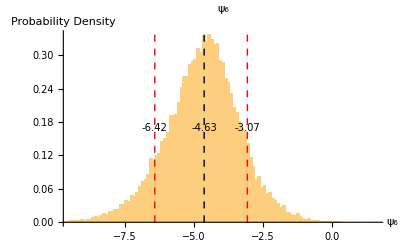

```mathematica
BCI["psi6"]=PlotParameterWithBCI[samples["psi6"],Subscript["ψ","6"]][[1]];
```

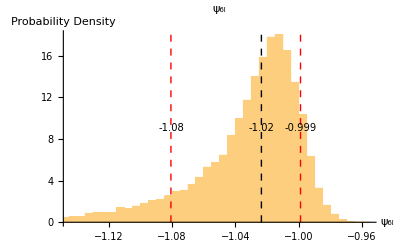

```mathematica
BCI["psi6l"]=PlotParameterWithBCI[samples["psi6l"],Subscript["ψ","6l"]][[1]];
```

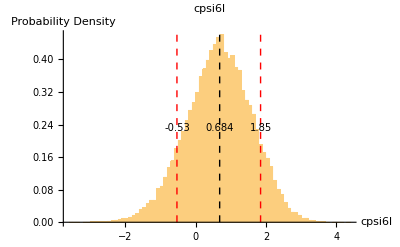

```mathematica
BCI[deviationName]=PlotParameterWithBCI[samples[deviationName],deviationName][[1]];
```

## Intersection

```mathematica
(*定义一个示例函数曲面*)surface=
Plot3D[
Function[{m1,m2},Psi[deviationOrder,η[m1,m2],M[m1,m2],BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]]][m1,m2],
{m1,20,100},
{m2,20,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=158.7,Red,Blue]&),
ColorFunctionScaling->False,
PlotStyle->{Opacity[0.6]},
PlotRange->All
];

(*定义z=0.5的常数平面*)
constantPlane1=Plot3D[BCI[deviationName][[1]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];
constantPlane2=Plot3D[BCI[deviationName][[2]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];
constantPlane3=Plot3D[BCI[deviationName][[3]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];

constantPlaneGR2=Plot3D[BCI[psiName][[2]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Black},Mesh->None];

(*组合显示两个图形*)
Show[surface,constantPlane1,constantPlane2,constantPlane3,constantPlaneGR2,PlotLabel->"3D曲面与z=0.5常数平面",AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Calculate Dots

IMRPhenomXPHM

### 2D, m_1-m_2, Fix two spin parameters

#### Set m_2-m_1 Axis

```mathematica
m2s=Range[BCI["mass2"][[1]]-10,BCI["mass2"][[3]]+10,0.1];
m1s=Range[BCI["mass1"][[1]]-10,BCI["mass1"][[3]]+10,0.1];
```

#### ψ_0 and ψ_2 Pancakes

```mathematica
pancakes=<||>;
```

```mathematica
pancakes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

```mathematica
pancakes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"m1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1-0.1),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"m1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1-0.01),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.1),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.01),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

#### ψ_0 and ψ_2 Non-GR Pancakes

```mathematica
pancakes[deviationName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[deviationName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Clear[pancakes]
```

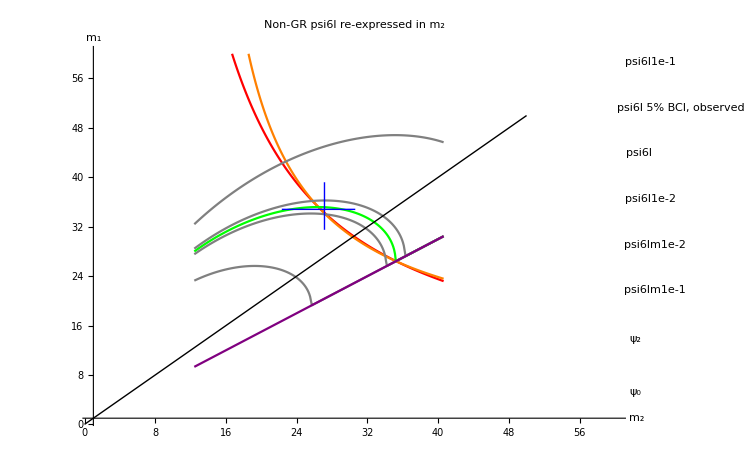

```mathematica
ListLinePlot[
{
Labeled[pancakes["psi0"][[2]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakes["psi2"][[2]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakes[psiName][[2]][[2;;]],psiName],

Labeled[pancakes[psiName<>"m1e-2"][[2]][[2;;]],psiName<>"m1e-2"],
Labeled[pancakes[psiName<>"m1e-1"][[2]][[2;;]],psiName<>"m1e-1"],
Labeled[pancakes[psiName<>"1e-2"][[2]][[2;;]],psiName<>"1e-2"],
Labeled[pancakes[psiName<>"1e-1"][[2]][[2;;]],psiName<>"1e-1"],

Labeled[pancakes[deviationName][[1]][[2;;]],psiName<>" 5% BCI, observed"],
Labeled[pancakes[deviationName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[deviationName][[3]][[2;;]],psiName<>" 95% BCI, observed"]
},
PlotStyle->{Red,Orange,Green,Gray,Gray,Gray,Gray,Purple,Purple,Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","2"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]},
PlotRange->{{1,60},{1,60}}
]
```

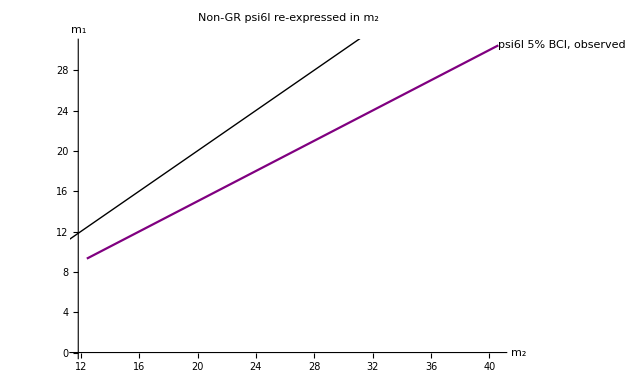

```mathematica
ListLinePlot[
{
Labeled[pancakes[deviationName][[1]][[2;;]],psiName<>" 5% BCI, observed"],
Labeled[pancakes[deviationName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[deviationName][[3]][[2;;]],psiName<>" 95% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","2"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]}
]
```

### 3D, χ_s-χ_a-η

```mathematica
chiss=Range[BCI["chis"][[1]],BCI["chis"][[2]],1/50];
chias=Range[BCI["chia"][[1]],BCI["chia"][[2]],1/50];
```

```mathematica
pancakes[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss,chias},{2,3},(* axes_,axesIndices_ *)
{deviationOrder},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &];
```

Set::wrsym: Symbol Depth is Protected.

```mathematica
ListPlot3D[
{
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &]
(*,Select[Flatten[pancakes[alphaName][[2]],Depth=1],Im[#[[3]]]==0 &]*)
(*,Select[Flatten[pancakes[alphaName][[3]],Depth=1],Im[#[[3]]]==0 &]*)
},
PlotRange->{{BCI["chis"][[1]],BCI["chis"][[3]]},{BCI["chia"][[1]],BCI["chia"][[3]]},{BCI["eta"][[1]],BCI["eta"][[3]]}}
]
```

Set::wrsym: Symbol Depth is Protected.

-Graphics3D-

```mathematica
pancakesFixChia[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
pancakesFixChia[modifiedAlphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[modifiedAlphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesFixChia[modifiedAlphaName]
```

{{{-0.176261,-2.23601},{-0.156261,-2.63373},{-0.136261,-3.13345},{-0.116261,-3.78142},{-0.0962614,-4.65754},{-0.0762614,-5.91358},{-0.0562614,-7.88009}},{{-0.176261,-0.515673},{-0.156261,-0.705506},{-0.136261,-0.942205},{-0.116261,-1.24574},{-0.0962614,-1.64989},{-0.0762614,-2.21694},{-0.0562614,-3.07708}},{{-0.176261,0.287298+3.5425×10^-15 ⅈ},{-0.156261,0.280539+2.72387×10^-15 ⅈ},{-0.136261,0.273704+3.80329×10^-15 ⅈ},{-0.116261,0.26679+2.26418×10^-15 ⅈ},{-0.0962614,0.259798+3.88682×10^-15 ⅈ},{-0.0762614,0.252725+1.98253×10^-15 ⅈ},{-0.0562614,0.22858}}}

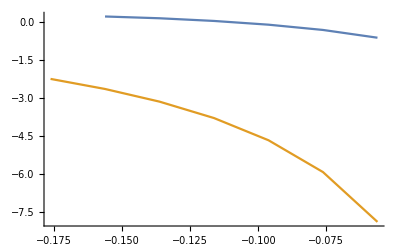

```mathematica
ListLinePlot[
{
Select[pancakesFixChia[alphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[3]],Im[#[[2]]]==0 &]
}
(*,PlotRange->{{-0.3,0},{0,1/4}}*)
]
```